```mathematica
Table[
```

```mathematica
allGraphs6FakeKeys2=RetrieveSortedKeys[allGraphs6,"colofournull"];Length[allGraphs6FakeKeys2]
```

203

```mathematica
allGraphs6AtomKeys=RetrieveSortedKeys[allGraphs6,"colofour"];Length[allGraphs6AtomKeys]
```

203

```mathematica
fakeVars=Table[allGraphs6[k,"colofournull"],{k,allGraphs6FakeKeys2}]
```

{p1x2x3x4x5x6,p12x3x4x5x6,p13x2x4x5x6,p14x2x3x5x6,p15x2x3x4x6,p16x2x3x4x5,p1x23x4x5x6,p1x24x3x5x6,p1x25x3x4x6,p1x26x3x4x5,p1x2x34x5x6,p1x2x35x4x6,p1x2x36x4x5,p1x2x3x45x6,p1x2x3x46x5,p1x2x3x4x56,p123x4x5x6,p124x3x5x6,p125x3x4x6,p126x3x4x5,p12x34x5x6,p12x35x4x6,p12x36x4x5,p12x3x45x6,p12x3x46x5,p12x3x4x56,p134x2x5x6,p135x2x4x6,p136x2x4x5,p13x24x5x6,p13x25x4x6,p13x26x4x5,p13x2x45x6,p13x2x46x5,p13x2x4x56,p145x2x3x6,p146x2x3x5,p14x23x5x6,p14x25x3x6,p14x26x3x5,p14x2x35x6,p14x2x36x5,p14x2x3x56,p156x2x3x4,p15x23x4x6,p15x24x3x6,p15x26x3x4,p15x2x34x6,p15x2x36x4,p15x2x3x46,p16x23x4x5,p16x24x3x5,p16x25x3x4,p16x2x34x5,p16x2x35x4,p16x2x3x45,p1x234x5x6,p1x235x4x6,p1x236x4x5,p1x23x45x6,p1x23x46x5,p1x23x4x56,p1x245x3x6,p1x246x3x5,p1x24x35x6,p1x24x36x5,p1x24x3x56,p1x256x3x4,p1x25x34x6,p1x25x36x4,p1x25x3x46,p1x26x34x5,p1x26x35x4,p1x26x3x45,p1x2x345x6,p1x2x346x5,p1x2x34x56,p1x2x356x4,p1x2x35x46,p1x2x36x45,p1x2x3x456,p1234x5x6,p1235x4x6,p1236x4x5,p123x45x6,p123x46x5,p123x4x56,p1245x3x6,p1246x3x5,p124x35x6,p124x36x5,p124x3x56,p1256x3x4,p125x34x6,p125x36x4,p125x3x46,p126x34x5,p126x35x4,p126x3x45,p12x345x6,p12x346x5,p12x34x56,p12x356x4,p12x35x46,p12x36x45,p12x3x456,p1345x2x6,p1346x2x5,p134x25x6,p134x26x5,p134x2x56,p1356x2x4,p135x24x6,p135x26x4,p135x2x46,p136x24x5,p136x25x4,p136x2x45,p13x245x6,p13x246x5,p13x24x56,p13x256x4,p13x25x46,p13x26x45,p13x2x456,p1456x2x3,p145x23x6,p145x26x3,p145x2x36,p146x23x5,p146x25x3,p146x2x35,p14x235x6,p14x236x5,p14x23x56,p14x256x3,p14x25x36,p14x26x35,p14x2x356,p156x23x4,p156x24x3,p156x2x34,p15x234x6,p15x236x4,p15x23x46,p15x246x3,p15x24x36,p15x26x34,p15x2x346,p16x234x5,p16x235x4,p16x23x45,p16x245x3,p16x24x35,p16x25x34,p16x2x345,p1x2345x6,p1x2346x5,p1x234x56,p1x2356x4,p1x235x46,p1x236x45,p1x23x456,p1x2456x3,p1x245x36,p1x246x35,p1x24x356,p1x256x34,p1x25x346,p1x26x345,p1x2x3456,p12345x6,p12346x5,p1234x56,p12356x4,p1235x46,p1236x45,p123x456,p12456x3,p1245x36,p1246x35,p124x356,p1256x34,p125x346,p126x345,p12x3456,p13456x2,p1345x26,p1346x25,p134x256,p1356x24,p135x246,p136x245,p13x2456,p1456x23,p145x236,p146x235,p14x2356,p156x234,p15x2346,p16x2345,p1x23456,p123456}

```mathematica
BaseCoeff6[key_]:=Table[Coefficient[allGraphs6[key,"colofournull"],var],{var,fakeVars}]
```

```mathematica
fullVars=Table[allGraphs6[k,"colofour"],{k,allGraphs6AtomKeys}]
```

{v1x2x3x4x5x6,v1x2x3x4x56,v1x2x3x46x5,v1x2x3x45x6,v1x2x3x456,v1x2x36x4x5,v1x2x36x45,v1x2x35x4x6,v1x2x35x46,v1x2x356x4,v1x2x34x5x6,v1x2x34x56,v1x2x346x5,v1x2x345x6,v1x2x3456,v1x26x3x4x5,v1x26x3x45,v1x26x35x4,v1x26x34x5,v1x26x345,v1x25x3x4x6,v1x25x3x46,v1x25x36x4,v1x25x34x6,v1x25x346,v1x256x3x4,v1x256x34,v1x24x3x5x6,v1x24x3x56,v1x24x36x5,v1x24x35x6,v1x24x356,v1x246x3x5,v1x246x35,v1x245x3x6,v1x245x36,v1x2456x3,v1x23x4x5x6,v1x23x4x56,v1x23x46x5,v1x23x45x6,v1x23x456,v1x236x4x5,v1x236x45,v1x235x4x6,v1x235x46,v1x2356x4,v1x234x5x6,v1x234x56,v1x2346x5,v1x2345x6,v1x23456,v16x2x3x4x5,v16x2x3x45,v16x2x35x4,v16x2x34x5,v16x2x345,v16x25x3x4,v16x25x34,v16x24x3x5,v16x24x35,v16x245x3,v16x23x4x5,v16x23x45,v16x235x4,v16x234x5,v16x2345,v15x2x3x4x6,v15x2x3x46,v15x2x36x4,v15x2x34x6,v15x2x346,v15x26x3x4,v15x26x34,v15x24x3x6,v15x24x36,v15x246x3,v15x23x4x6,v15x23x46,v15x236x4,v15x234x6,v15x2346,v156x2x3x4,v156x2x34,v156x24x3,v156x23x4,v156x234,v14x2x3x5x6,v14x2x3x56,v14x2x36x5,v14x2x35x6,v14x2x356,v14x26x3x5,v14x26x35,v14x25x3x6,v14x25x36,v14x256x3,v14x23x5x6,v14x23x56,v14x236x5,v14x235x6,v14x2356,v146x2x3x5,v146x2x35,v146x25x3,v146x23x5,v146x235,v145x2x3x6,v145x2x36,v145x26x3,v145x23x6,v145x236,v1456x2x3,v1456x23,v13x2x4x5x6,v13x2x4x56,v13x2x46x5,v13x2x45x6,v13x2x456,v13x26x4x5,v13x26x45,v13x25x4x6,v13x25x46,v13x256x4,v13x24x5x6,v13x24x56,v13x246x5,v13x245x6,v13x2456,v136x2x4x5,v136x2x45,v136x25x4,v136x24x5,v136x245,v135x2x4x6,v135x2x46,v135x26x4,v135x24x6,v135x246,v1356x2x4,v1356x24,v134x2x5x6,v134x2x56,v134x26x5,v134x25x6,v134x256,v1346x2x5,v1346x25,v1345x2x6,v1345x26,v13456x2,v12x3x4x5x6,v12x3x4x56,v12x3x46x5,v12x3x45x6,v12x3x456,v12x36x4x5,v12x36x45,v12x35x4x6,v12x35x46,v12x356x4,v12x34x5x6,v12x34x56,v12x346x5,v12x345x6,v12x3456,v126x3x4x5,v126x3x45,v126x35x4,v126x34x5,v126x345,v125x3x4x6,v125x3x46,v125x36x4,v125x34x6,v125x346,v1256x3x4,v1256x34,v124x3x5x6,v124x3x56,v124x36x5,v124x35x6,v124x356,v1246x3x5,v1246x35,v1245x3x6,v1245x36,v12456x3,v123x4x5x6,v123x4x56,v123x46x5,v123x45x6,v123x456,v1236x4x5,v1236x45,v1235x4x6,v1235x46,v12356x4,v1234x5x6,v1234x56,v12346x5,v12345x6,v123456}

```mathematica
BaseCoeff6F[key_]:=Table[Coefficient[allGraphs6[key,"colofour"],var],{var,fullVars}]
```

```mathematica
done=0;Monitor[
Table[
done++;
allGraphs6[k,"colofournull"]=Simplify[allGraphs6[k,"colofournull"]],
{k,allGraphs6AtomKeys}
],{done,Length[allGraphs6[k,"colofournull"]]}];
```

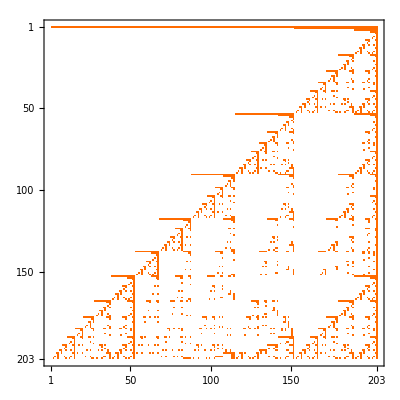

```mathematica
Table[BaseCoeff6F[k],{k,allGraphs6NullAtomKeys}]//MatrixPlot
```

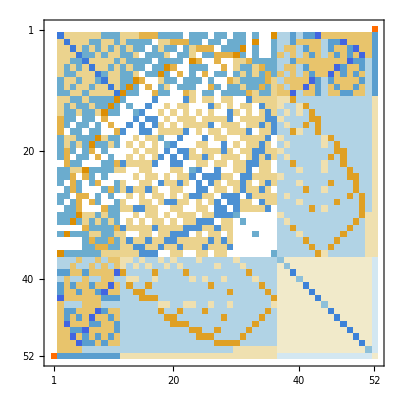

```mathematica
MatrixPlot[ConversionMatrix["C","F"]]
```

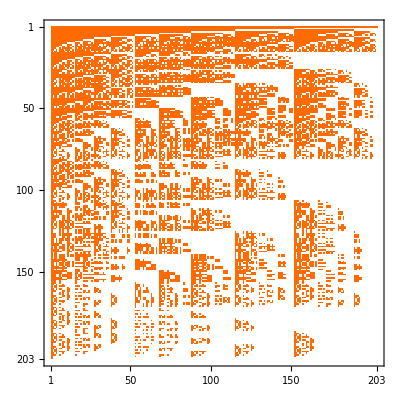

```mathematica
Table[BaseCoeff6F[k],{k,allGraphs6FakeKeys2}]//MatrixPlot
```

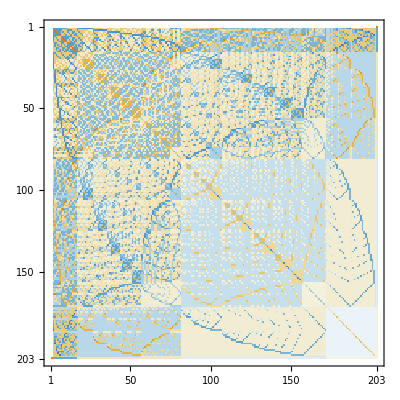

```mathematica
Table[BaseCoeff6[k],{k,allGraphs6AtomKeys}]//MatrixPlot
```

```mathematica
Table[BaseCoeff6F[k],{k,allGraphs6FakeKeys2}]//MatrixPlot
```

-Graphics-

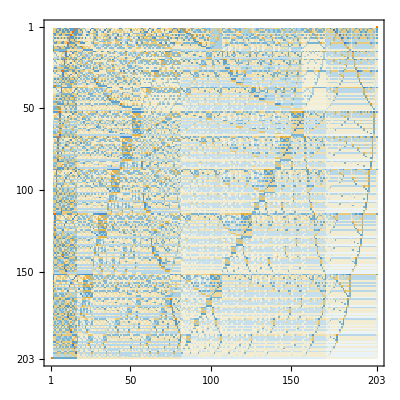

```mathematica
Table[BaseCoeff6[k],{k,allGraphs6AtomKeys}]//MatrixPlot
```